```mathematica
PATHL10="/Users/diego/Documents/Proyecto-Computacional/Ising/Ising_DATA_cuadrado_L10_MC50000_T1.0000_3.5000/data.csv";
PATHL20="/Users/diego/Documents/Proyecto-Computacional/Ising/Ising_DATA_cuadrado_L20_MC50000_T1.0000_3.5000/data.csv";
PATHL50="/Users/diego/Documents/Proyecto-Computacional/Ising/Ising_DATA_cuadrado_L50_MC50000_T1.0000_3.5000/data.csv";
PATHL100="/Users/diego/Documents/Proyecto-Computacional/Ising/Ising_DATA_cuadrado_L100_MC50000_T1.0000_3.5000/data.csv";

PATHL1501="/Users/diego/Documents/Proyecto-Computacional/Ising/Ising_DATA_cuadrado_L150_MC50000_T1.9900_2.2800/data.csv";
PATHL1502="/Users/diego/Documents/Proyecto-Computacional/Ising/Ising_DATA_cuadrado_L150_MC50000_T1.3600_1.6500/data.csv";
PATHL1503="/Users/diego/Documents/Proyecto-Computacional/Ising/Ising_DATA_cuadrado_L150_MC50000_T1.0000_3.5500/data.csv";
```

```mathematica
Datos10 = Import[PATHL10];
Datos20 = Import[PATHL20];
Datos50 = Import[PATHL50];
Datos100 = Import[PATHL100];

Datos1501 = Import[PATHL1501];
Datos1502 = Import[PATHL1502];
Datos1503 = Import[PATHL1503];
```

```mathematica
Datos10[[1]]
```

{T,E,M,M_abs,Cv,Chim,Chim_abs}

```mathematica
MagnetizacionAbsL10 =Table[{Datos10[[i,1]],Datos10[[i,4]]},{i,1,Length[Datos10]}];
MagnetizacionAbsL20 =Table[{Datos20[[i,1]],Datos20[[i,4]]},{i,1,Length[Datos20]}];
MagnetizacionAbsL50 =Table[{Datos50[[i,1]],Datos50[[i,4]]},{i,1,Length[Datos50]}];
MagnetizacionAbsL100 =Table[{Datos100[[i,1]],Datos100[[i,4]]},{i,1,Length[Datos100]}];

MagnetizacionL10 =Table[{Datos10[[i,1]],Datos10[[i,3]]},{i,1,Length[Datos10]}];
MagnetizacionL20 =Table[{Datos20[[i,1]],Datos20[[i,3]]},{i,1,Length[Datos20]}];
MagnetizacionL50 =Table[{Datos50[[i,1]],Datos50[[i,3]]},{i,1,Length[Datos50]}];
MagnetizacionL100 =Table[{Datos100[[i,1]],Datos100[[i,3]]},{i,1,Length[Datos100]}];

ChimAbsL10 =Table[{Datos10[[i,1]],Datos10[[i,7]]},{i,1,Length[Datos10]}];
ChimAbsL20 =Table[{Datos20[[i,1]],Datos20[[i,7]]},{i,1,Length[Datos20]}];
ChimAbsL50 =Table[{Datos50[[i,1]],Datos50[[i,7]]},{i,1,Length[Datos50]}];
ChimAbsL100 =Table[{Datos100[[i,1]],Datos100[[i,7]]},{i,1,Length[Datos100]}];

ChimL10 =Table[{Datos10[[i,1]],Datos10[[i,6]]},{i,1,Length[Datos10]}];
ChimL20 =Table[{Datos20[[i,1]],Datos20[[i,6]]},{i,1,Length[Datos20]}];
ChimL50 =Table[{Datos50[[i,1]],Datos50[[i,6]]},{i,1,Length[Datos50]}];
ChimL100 =Table[{Datos100[[i,1]],Datos100[[i,6]]},{i,1,Length[Datos100]}];

CvL10 =Table[{Datos10[[i,1]],Datos10[[i,5]]},{i,1,Length[Datos10]}];
CvL20 =Table[{Datos20[[i,1]],Datos20[[i,5]]},{i,1,Length[Datos20]}];
CvL50 =Table[{Datos50[[i,1]],Datos50[[i,5]]},{i,1,Length[Datos50]}];
CvL100 =Table[{Datos100[[i,1]],Datos100[[i,5]]},{i,1,Length[Datos100]}];


MagnetizacionAbsL1501 =Table[{Datos1501[[i,1]],Datos1501[[i,3]]},{i,1,Length[Datos1501]}];
MagnetizacionAbsL1502 =Table[{Datos1502[[i,1]],Datos1502[[i,3]]},{i,1,Length[Datos1502]}];
MagnetizacionAbsL1503 =Table[{Datos1503[[i,1]],Datos1503[[i,3]]},{i,1,Length[Datos1503]}];
```

```mathematica
Rasterize[ListPlot[{MagnetizacionL10,MagnetizacionL20,MagnetizacionL50, MagnetizacionL100},Frame->True, GridLines->Automatic,FrameLabel->{"T","Magnetización"}, PlotLegends->{"10","20","50","100"}, ImageSize->Large]]
```

-Graphics-

```mathematica
Rasterize[ListPlot[{MagnetizacionAbsL10,MagnetizacionAbsL20,MagnetizacionAbsL50, MagnetizacionAbsL100}, Frame->True, GridLines->Automatic,FrameLabel->{"T","Magnetización"}, PlotLegends->{"10","20","50","100"}, ImageSize->Large]]
```

-Graphics-

```mathematica
Rasterize[ListLogPlot[{CvL10,CvL20,CvL50, CvL100}, Frame->True, GridLines->Automatic,FrameLabel->{"T","C_H"}, PlotLegends->{"10","20","50","100"}, ImageSize->Large]]
```

-Graphics-

```mathematica
Rasterize[ListLogPlot[{ChimAbsL10,ChimAbsL20,ChimAbsL50, ChimAbsL100}, Frame->True, GridLines->Automatic,FrameLabel->{"T","χ_M"}, PlotLegends->{"10","20","50","100"}, ImageSize->Large]]
```

-Graphics-

```mathematica
Rasterize[ListLogPlot[{ChimL10,ChimL20,ChimL50, ChimL100}, Frame->True, GridLines->Automatic,FrameLabel->{"T","χ_M"}, PlotLegends->{"10","20","50","100"}, ImageSize->Large]]
```

-Graphics-

```mathematica
Datos1501 = Import[PATHL1501];
Datos1502 = Import[PATHL1502];
Datos1503 = Import[PATHL1503];
```

```mathematica
MagnetizacionAbsL1501 =Table[{Datos1501[[i,1]],Datos1501[[i,3]]},{i,1,Length[Datos1501]}];
MagnetizacionAbsL1502 =Table[{Datos1502[[i,1]],Datos1502[[i,3]]},{i,1,Length[Datos1502]}];
MagnetizacionAbsL1503 =Table[{Datos1503[[i,1]],Datos1503[[i,3]]},{i,1,Length[Datos1503]}];
```

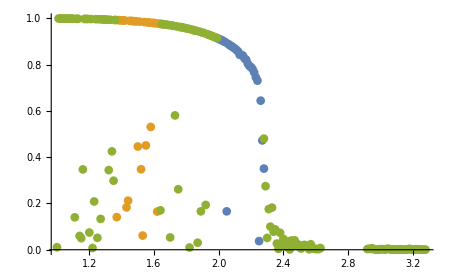

```mathematica
ListPlot[{MagnetizacionAbsL1501,MagnetizacionAbsL1502,MagnetizacionAbsL1503}]
```

```mathematica
PATHCorr="/Volumes/A LA VERDE/Ising/Ising_DATA_cuadrado_L100_MC50000_T1.0000_3.5000/correlacion.csv";
```

```mathematica
DatosCorr = Import[PATHCorr];
```

```mathematica
DatosCorr[[1]]
```

{T,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
Export["/Users/diego/Documents/Proyecto-Computacional/Ising/Corr.gif",Table[ListLogLinearPlot[Table[{DatosCorr[[1,i]],DatosCorr[[n,i]]},{i, 2,51}], ImageSize->Large,Frame->True,PlotLabel->"T = " +DatosCorr[[n,1]],FrameLabel->{"Ln(r)","ξ"}, GridLines->Automatic,PlotRange->{-0.1,1.1}],{n,1,200,1}], "gif"]
```

/Users/diego/Documents/Proyecto-Computacional/Ising/Corr.gif